Testing Radiation Dose vs Solid Cancer Rate Models

Data:

```mathematica
n=10; (*# data pts*)
(*data's row format: {x,y,total length of error bars}*)
datainch={{0.13,0,0.31},{0.63,0.19,0.50},{1.31,0.75,0.63},{2.13,0.50,1.25},{2.63,1.19,1.13},{3.63,2.25,1.50},{4.69,3.38,2.19},{5.75,2.69,2.38},{6.75,4.38,3.69},{7.81,4.69,4.63}}; 
(*Conversion from inches to values of the actual data pts*)
xconv = 1/4.2;  (*inches -> dose in Sv*)
yconv = 1/4.2; (*inches -> excess relative risk (ERR)*)
errconv = yconv/4; (*inches -> st. dev. of ERR*)
(*Convert data*)
datapts=Table[{Round[datainch[[i,1]]*xconv,0.001],Round[datainch[[i,2]]*yconv,0.001]},{i,1,n}];
stdev=Table[Round[datainch[[i,3]]*errconv,0.001],{i,1,n}];
Grid[Join[{{"Data from Solid Cancer Plot",SpanFromLeft},{"","Radiation Dose (Sv)","Excess Relative Risk (ERR)","St.Dev. of ERR"}},Table[{ToString[i]<>".",datapts[[i,1]],datapts[[i,2]],stdev[[i]]},{i,1,n}]],Frame->All]
```

Data from Solid Cancer Plot |  |  | 
 | Radiation Dose (Sv) | Excess Relative Risk (ERR) | St.Dev. of ERR
1. | 0.031 | 0. | 0.018
2. | 0.15 | 0.045 | 0.03
3. | 0.312 | 0.179 | 0.038
4. | 0.507 | 0.119 | 0.074
5. | 0.626 | 0.283 | 0.067
6. | 0.864 | 0.536 | 0.089
7. | 1.117 | 0.805 | 0.13
8. | 1.369 | 0.64 | 0.142
9. | 1.607 | 1.043 | 0.22
10. | 1.86 | 1.117 | 0.276

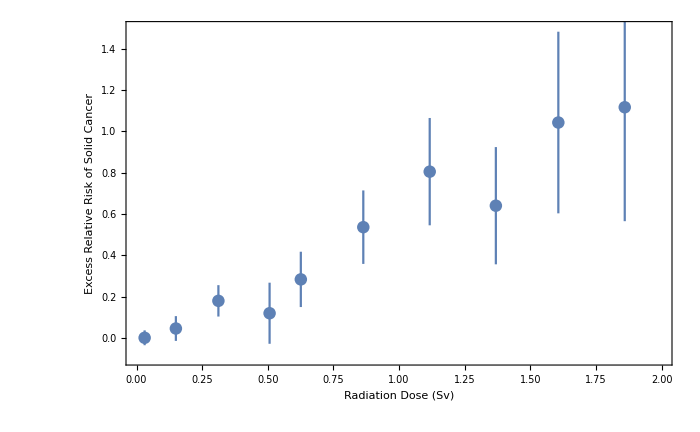

```mathematica
(*Plot Data*)
Needs["ErrorBarPlots`"]
datawitherror=Table[{datapts[[i]],ErrorBar[2*stdev[[i]]]},{i,1,n}];
dataplot=ErrorListPlot[datawitherror,PlotRange->{{0,2.0},{-0.1,1.5}},Frame->True,Axes->False,FrameLabel->{"Radiation Dose (Sv)", "Excess Relative Risk of Solid Cancer"},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"}]
```

Linear Relationship Fit

```mathematica
fitLR[x_,lambda_]:=lambda*x
```

Maximum Likelihood Estimate

```mathematica
y=datapts[[All,2]];
chisqLR[lambda_]:=1/4*Total[(y-fitLR[datapts[[All,1]],lambda])^2/stdev^2]
MLE=lambda/.Last[FindMinimum[chisqLR[lambda],lambda]]
LRminCHI=chisqLR[MLE]
```

0.532207

2.92594

MLE Variance and Goodness-of-fit

```mathematica
(*List of "Means" for solid cancer rate distributions*)
ymean=fitLR[datapts[[All,1]],MLE];
(*Simulate Data*)
MLEsim={};
CHIsim={};
samplenum=1000;
For[j=0,j<samplenum,j++,ysim=Array[0,n];For[k=1,k<n+1,k++,ysim[[k]]=RandomVariate[NormalDistribution[ymean[[k]],stdev[[k]]]]];
(*Find MLE...*)
y=ysim;AppendTo[MLEsim,lambda/.Last[FindMinimum[chisqLR[lambda],lambda]]];
(*Find Min Chi^2...*)
AppendTo[CHIsim,chisqLR[MLEsim[[j+1]]]]]
```

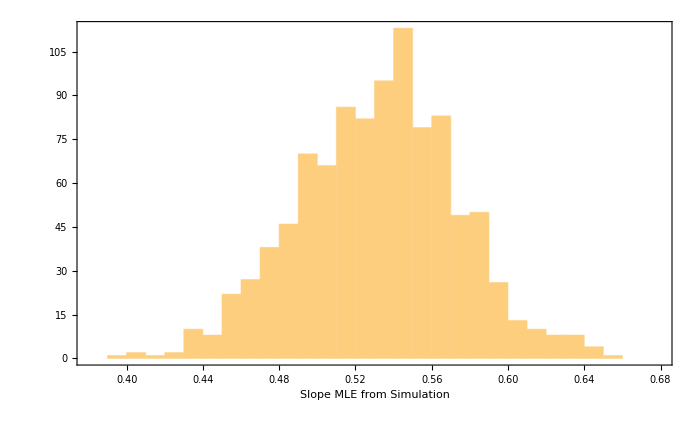

0.0414843

```mathematica
(*Calculate Standard Deviation*)
Histogram[MLEsim,{0.38,0.68,0.01},Frame->True,Axes->False,FrameLabel->{"Slope MLE from Simulation", ""},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"}]
varMLE=(1/samplenum)*Sum[(MLEsim[[i]]-MLE)^2,{i,1,samplenum}];
stdevMLE=Sqrt[varMLE]
```

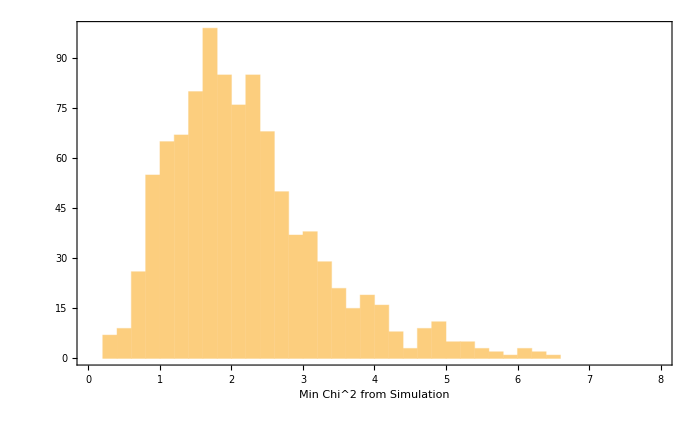

0.796

```mathematica
(*Determine Goodness-of-fit = fraction of CHIsim that are </= minCHI*)
Histogram[CHIsim,{0,8,0.2},Frame->True,Axes->False,FrameLabel->{"Min Chi^2 from Simulation", ""},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"}]
pLR=Count[CHIsim,chi_/; chi<LRminCHI]/samplenum//N
```

Plot of LR Fit

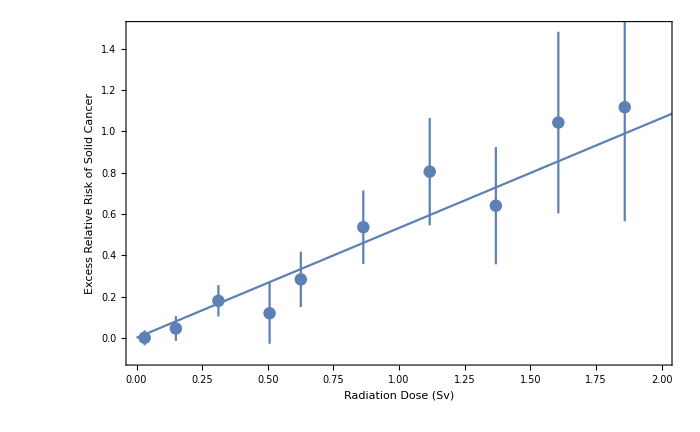

```mathematica
LRfitplot=Plot[fitLR[x,MLE],{x,0,8.5}];
Show[dataplot,LRfitplot]
```

Delayed Effects Fit

```mathematica
fitDE[x_,lambda1_,lambda2_]:=Piecewise[{{lambda1*x-lambda2,x≥lambda2/lambda1}},0] 
fitline[x_,lambda1_,lambda2_]:=lambda1*x-lambda2
```

Maximum Likelihood Estimate

```mathematica
y=datapts[[All,2]];
chisqDE[lambda1_Real,lambda2_Real]:=1/4*Sum[(y[[i]]-fitDE[datapts[[i,1]],lambda1,lambda2])^2/stdev[[i]]^2,{i,1,n}]
fit=FindMinimum[chisqDE[lambda1,lambda2],{lambda1,lambda2}];
MLE1=lambda1/.fit[[2]]
MLE2=lambda2/.fit[[2]]
DEminCHI=fit[[1]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.60588

0.0454703

2.17276

```mathematica
Plot3D[chisqDE[lambda1,lambda2],{lambda1,0.4,0.95},{lambda2,0,0.2}]
```

-Graphics3D-

MLE Variance and Goodness-of-fit

```mathematica
(*List of "Means" for solid cancer rate distributions*)
ymean=Array[0,n];
For[j=1,j<n+1,j++,ymean[[j]]=fitDE[datapts[[j,1]],MLE1,MLE2]]
(*Simulate Data*)
MLE1sim={};
MLE2sim={};
CHIsim={};
samplenum=1000;
For[j=0,j<samplenum,j++,ysim=Array[0,n];For[k=1,k<n+1,k++,ysim[[k]]=RandomVariate[NormalDistribution[ymean[[k]],stdev[[k]]]]];
(*Find MLEs...*)
y=ysim;simfit=FindMinimum[{chisqDE[lambda1,lambda2]},{{lambda1,0.6},{lambda2,0.05}}];(*simfit2=FindMinimum[{chisqDE[lambda1,lambda2],lambda2≥0},{{lambda1,0.6},{lambda2,0.005}}];
simfit=If[simfit1[[1]]<simfit2[[1]],simfit1,simfit2];*)
AppendTo[MLE1sim,lambda1/.simfit[[2]]]; AppendTo[MLE2sim,lambda2/.simfit[[2]]];
(*Find Min Chi^2...*) 
AppendTo[CHIsim,simfit[[1]]]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

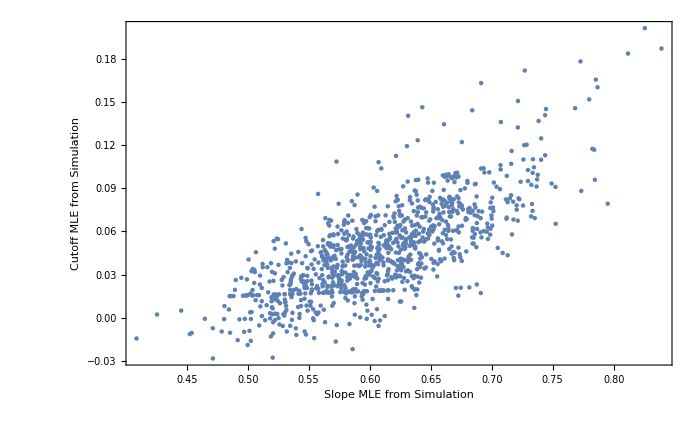

0.0624919

0.0319454

```mathematica
(*Calculate Standard Deviation*)
ListPlot[Table[{MLE1sim[[i]],MLE2sim[[i]]},{i,1,samplenum}],Frame->True,Axes->False,FrameLabel->{"Slope MLE from Simulation", "Cutoff MLE from Simulation"},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"}]
varMLE1=(1/samplenum)*Sum[(MLE1sim[[i]]-MLE1)^2,{i,1,samplenum}];
varMLE2=(1/samplenum)*Sum[(MLE2sim[[i]]-MLE2)^2,{i,1,samplenum}];
stdevMLE1=Sqrt[varMLE1]
stdevMLE2=Sqrt[varMLE2]
```

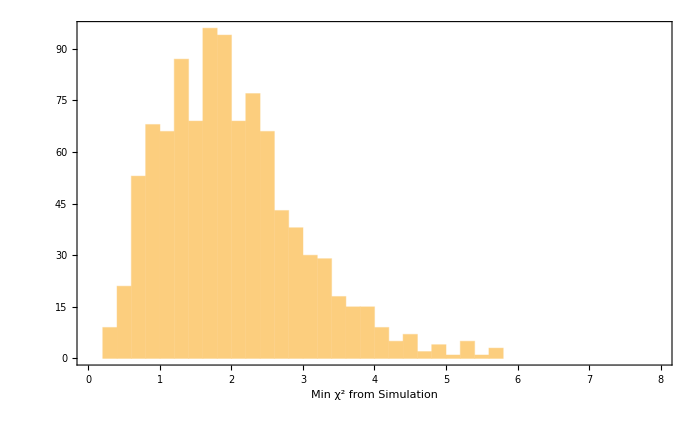

0.625

```mathematica
(*Determine Goodness-of-fit = fraction of CHIsim that are </= minCHI*)
Histogram[CHIsim,{0,8,0.2},Frame->True,Axes->False,FrameLabel->{"Min χ^2 from Simulation", ""},LabelStyle->Bold,ImageSize->700,BaseStyle->{FontSize->16, FontFamily->"Helvetica"}]
pDE=Count[CHIsim,chi_/; chi<DEminCHI]/samplenum//N
```

Plot of DE Fit

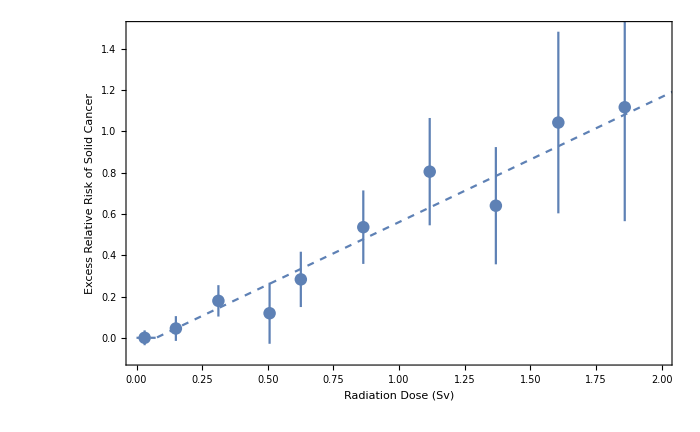

```mathematica
DEfitplot=Plot[fitDE[x,MLE1,MLE2],{x,0,8.5},PlotStyle->Dashed];
Show[dataplot,DEfitplot]
```

Comparing Fits

Plot

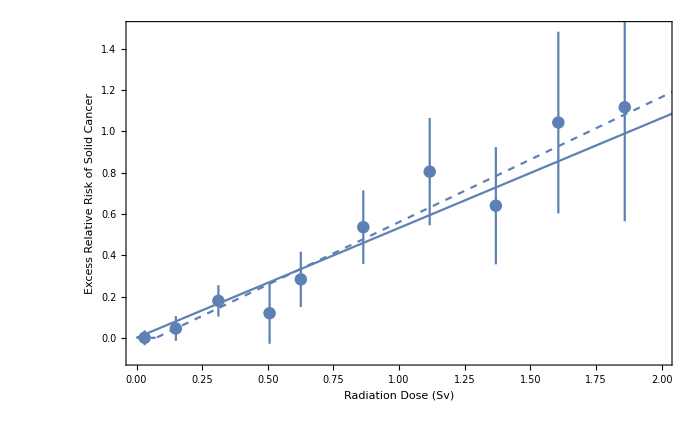

```mathematica
Show[dataplot,LRfitplot,DEfitplot]
```

Summary Table

```mathematica
Grid[{{Text["Fit Comparison"],SpanFromLeft},{"","Linear Relationship","Delayed Effects"},{"Best Fit Curve",Round[MLE,0.01]*x,ToString[Round[MLE1,0.01]]<>"x-"<>ToString[Round[MLE2,0.01]]},{"St. Dev.",Round[stdevMLE,0.01],ToString[Round[stdevMLE1,0.01]]<>","<>ToString[Round[stdevMLE2,0.01]]},{"Goodness-of-fit",pLR,pDE}},Frame->All]
```

Fit Comparison |  | 
 | Linear Relationship | Delayed Effects
Best Fit Curve | x Round[MLE,0.01] | 0.61x-0.05
St. Dev. | Round[stdevMLE,0.01] | 0.06,0.03
Goodness-of-fit | pLR | 0.625